```mathematica
2.670143*Exp[−1.500258*z]*Cos[0.346731*z]−0.458705*Exp[−4.125588*z]*Cos[1.390912*z]−1.211438*Exp[−1.744602*z]* Cos[1.798436z]
```

2.67014 ⅇ^(-1.50026 z) Cos[0.346731 z]-0.458705 ⅇ^(-4.12559 z) Cos[1.39091 z]-1.21144 ⅇ^(-1.7446 z) Cos[1.79844 z]

```mathematica
FourierTransform[2.670143*Exp[−1.500258*Abs[t]]*Cos[0.346731*t]−0.458705*Exp[−4.125588*Abs[t]]*Cos[1.390912*t]−1.211438*Exp[−1.744602*Abs[t]]* Cos[1.798436t],t,ω]
```

((79592.1+0. ⅈ)+(26745.7+0. ⅈ) ω^2-(3287.76+0. ⅈ) ω^4+(90.068+0. ⅈ) ω^6-(0.334915+0. ⅈ) ω^8-(1.28006×10^-6+0. ⅈ) ω^10)/((79608.3+0. ⅈ)+(66256.4+0. ⅈ) ω^2+(20820.9+0. ⅈ) ω^4+(2869.48+0. ⅈ) ω^6+(519.761+0. ⅈ) ω^8+(34.0513+0. ⅈ) ω^10+(1.+0. ⅈ) ω^12)

```mathematica
Simplify[%]
```

((79592.1+0. ⅈ)+(26745.7+0. ⅈ) ω^2-(3287.76+0. ⅈ) ω^4+(90.068+0. ⅈ) ω^6-(0.334915+0. ⅈ) ω^8-(1.28006×10^-6+0. ⅈ) ω^10)/((79608.3+0. ⅈ)+(66256.4+0. ⅈ) ω^2+(20820.9+0. ⅈ) ω^4+(2869.48+0. ⅈ) ω^6+(519.761+0. ⅈ) ω^8+(34.0513+0. ⅈ) ω^10+(1.+0. ⅈ) ω^12)

```mathematica
InputForm[%]
```

```mathematica
(79592.09638611815  + 26745.70269067656*ω^2 - 
  3287.7641971961766*ω^4 + 90.06796627903168*ω^6 - 
  0.33491524736443523*ω^8 - 1.2800637532173198*10^(-6)*ω^10)/
 (79608.29049745783 + 66256.38975543922*ω^2 + 
  20820.912138378146*ω^4 + 2869.475412460314*ω^6 + 
  519.7608141080697*ω^8 + 34.051311853022*ω^10 + ω^12)
```

(79592.1+26745.7 ω^2-3287.76 ω^4+90.068 ω^6-0.334915 ω^8-1.28006×10^-6 ω^10)/(79608.3+66256.4 ω^2+20820.9 ω^4+2869.48 ω^6+519.761 ω^8+34.0513 ω^10+ω^12)

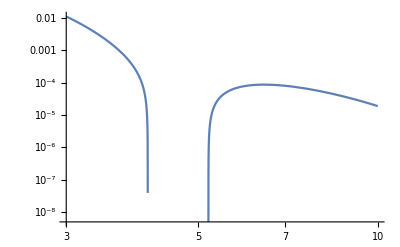

```mathematica
LogLogPlot[Out[6],{ω,3,10}]
```

```mathematica
FourierTransform[a*Exp[−b*Abs[t]]*Cos[c*t],t,ω]
```

a (b/(√(2 π) (b^2+c^2-2 c ω+ω^2))+b/(√(2 π) (b^2+(c+ω)^2)))

```mathematica
Simplify[%]
```

(a b √(2/π) (b^2+c^2+ω^2))/((b^2+(c-ω)^2) (b^2+(c+ω)^2))

```mathematica
FullSimplify[%]
```

(a b √(2/π) (b^2+c^2+ω^2))/((b^2+(c-ω)^2) (b^2+(c+ω)^2))

```mathematica
ExpandAll[%]
```

(a b^3 √(2/π))/(b^4+2 b^2 c^2+c^4+2 b^2 ω^2-2 c^2 ω^2+ω^4)+(a b c^2 √(2/π))/(b^4+2 b^2 c^2+c^4+2 b^2 ω^2-2 c^2 ω^2+ω^4)+(a b √(2/π) ω^2)/(b^4+2 b^2 c^2+c^4+2 b^2 ω^2-2 c^2 ω^2+ω^4)

```mathematica
Simplify[%]
```

(a b √(2/π) (b^2+c^2+ω^2))/(b^4+(c^2-ω^2)^2+2 b^2 (c^2+ω^2))

```mathematica
% /. c -> 0
```

(a b √(2/π) (b^2+ω^2))/(b^4+2 b^2 ω^2+ω^4)

```mathematica
Simplify[%]
```

(a b √(2/π))/(b^2+ω^2)